## Start

### Setup

#### Default options for plots, error messages, and colors

```mathematica
SetDirectory["/Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
```

SetDirectory::cdir: Cannot set current directory to /Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica.

#### Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN","S","mS"};
bI={"I1","I2","I","mI","N","mN","S","mS"};
bJ={"I1","mI1","I2","mI2","N","S","J","mJ"};
bIJ={"I1","I2","I","mI","N","S","J","mJ"};
bF={"I1","I2","I","N","S","J","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1","S","J"};
bF2={"I1","mI1","I2","N","F2","mF2","S","J"};
bN={"N","mN"};
bI1={"I1","mI1"};
bI2={"I2","mI2"};
bS={"S","mS"};
b={bUC,bI,bJ,bIJ,bF,bF1,bF2,bN};
```

#### Supporting functions

```mathematica
conj[x_]:=Module[{re,im},x/.(Complex[re_,im_]->Complex[re,-im])]; (*Replacement that gives the complex conjugate*)
createSpace[aQN_Association]:=Module[{a},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
nℋ=Sum[(2I1+1)(2I2+1)(2N+1)(2S+1),{N,a["N"]},{S,a["S"]},{I1,a["I1"]},{I2,a["I2"]}]; (*number of states in Hilbert space*)
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
nℋI1=(2a["I1"][[1]]+1);
nℋI2=(2a["I2"][[1]]+1);
nℋI=(2a["I1"][[1]]+1)(2a["I2"][[1]]+1);
nℋS=(2a["S"][[1]]+1);
nℋN=Sum[(2N+1),{N,a["N"]}];
ℋ=IdentityMatrix[nℋ];
ℋI1=IdentityMatrix[nℋI1];
ℋI2=IdentityMatrix[nℋI2];
ℋI=IdentityMatrix[nℋI];
ℋS=IdentityMatrix[nℋS];
ℋN=IdentityMatrix[nℋN];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
sℋI1=Partition[ℋI1,{nℋI1,1}][[1]];
sℋI2=Partition[ℋI2,{nℋI2,1}][[1]];
sℋI=Partition[ℋI,{nℋI,1}][[1]];
sℋS=Partition[ℋS,{nℋS,1}][[1]];
sℋN=Partition[ℋN,{nℋN,1}][[1]];
] (*example: aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->{0,1}]*)
```

```mathematica
createLists[aQN_Association]:=Module[{a,spins},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
am={{I1,a["I1"]},{I2,a["I2"]},{S,a["S"]},{N,a["N"]}}; (*angular momentums*)
lUC=Flatten[Table[ToExpression[bUC],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{mS,-S,S},{mN,-N,N}],7];
lI=Flatten[Table[ToExpression[bI],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{mN,-N,N},{mS,-S,S}],7];
lJ=Flatten[Table[ToExpression[bJ],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lIJ=Flatten[Table[ToExpression[bIJ],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lF=Flatten[Table[ToExpression[bF],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{J,Abs[N-S],N+S},{F,Abs[I-J],I+J},{mF,-F,F}],7];
lF1=Flatten[Table[ToExpression[bF1],Evaluate[Sequence@@am],{mI2,-I2,I2},{J,Abs[N-S],N+S},{F1,Abs[I1-J],I1+J},{mF1,-F1,F1}],7];
lF2=Flatten[Table[ToExpression[bF2],Evaluate[Sequence@@am],{mI1,-I1,I1},{J,Abs[N-S],N+S},{F2,Abs[I2-J],I2+J},{mF2,-F2,F2}],7];
lN=Flatten[Table[ToExpression[bN],{N,a["N"]},{mN,-N,N}],1];
l = {lUC,lI,lJ,lIJ,lF,lF1,lF2,lN};
BtoL = AssociationThread[b->l];
LtoB = AssociationThread[l->b];
StoLN=AssociationThread[sℋN->lN];
LtoSN=AssociationThread[lN->sℋN];
yN=lN/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
]
```

### Functions

```mathematica
eig[Hn_]:=Chop[Sort[Eigensystem[Hn]ᵀ]ᵀ];
reorder[list_,order_]:=Part[order,list];
VtoQN[eigenvector_,basis_:bUC,populationThreshold_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eigenvector,Abs[#]^2>=populationThreshold&],Abs];
sP=Position[eigenvector,#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,BtoL[basis][[sP]]}]
QNtoS[rep_,basis_:bUC]:=With[{labels=rep[[All,1]],numbers=rep[[All,2]]},Flatten[Position[BtoL[basis][[All,Flatten[labels/.PositionIndex[basis]]]],numbers]]]
QNtoV[rep_,eigenvectors_,basis_:bUC]:=Module[{pos,eigs},pos=QNtoS[rep];eigs=OrderingBy[eigenvectors[[All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];eigs]
reduceV[vecs_,param_,s_,rep_]:=Module[{pos,l},
pos=Flatten[Position[bUC,#]&/@rep[[All,1]]];
l=Transpose@{lUC[[All,pos]],Abs[vecs[[param,s]]]^2};
l=Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[l,First]];
l[[All,2]]
]
```

### Load

```mathematica
aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->Range[0,1]];
createSpace[aQN] (*creates a Hilbert space*)
createLists[aQN] (*creates a list of the quantum numbers of each basis state*)
HacN=Import["HacN.m"][[1;;Length[lN],1;;Length[lN]]]; 
(*needs to be multiplied by U*)
```

### Hamiltonians

#### Rotational Hamiltonian

```mathematica
HN=DiagonalMatrix[(#(#+1))&/@lN[[All,1]]]; (*needs to be multiplied by B*)
```

#### Interaction Hamiltonian

```mathematica
DME[{N_,M_},{Np_,Mp_},q_]:=(-1)^M √((2 N+1) (2 Np+1)) ThreeJSymbol[{N,-M},{1,q},{Np,Mp}] ThreeJSymbol[{N,0},{1,0},{Np,0}]
```

```mathematica
Dvec[{N_,M_},{Np_,Mp_}]:=Sum[(-1)^q{{1/(√2),-ⅈ/(√2),0},{0,0,1},{-1/(√2),-ⅈ/(√2),0}}[[q+2]]DME[{N,M},{Np,Mp},q],{q,-1,1}]
ℰ=Normalize[{5,5,3}]Cos[2π f t];
```

```mathematica
Hint=Table[Ω Dvec[lN[[i]],lN[[j]]].ℰ,{i,1,Length[lN]},{j,1,Length[lN]}];
```

```mathematica
νtab=Table[Switch[lN[[i,1]],0,0,1,f],{i,nℋN}]
u=MatrixExp[-ⅈ 2π t DiagonalMatrix[νtab]];
```

{0,f,f,f}

```mathematica
consts={θh->0*(π/2-1/2 ArcCos[1/(√3)]),θq->π/2-ArcCos[1/(√3)],αpar->1872.1153,αperp->467.0375,U->1 10^6,B->3.4761/2 10^9};
H0=(2π B HN+2π U HacN/.consts);
```

```mathematica
HLF=H0+(Hint/.Ω->2π  1/(9.55 10^-6));
```

```mathematica
HRF=TrigToExp[ComplexExpand[u†.HLF.u-ⅈ u†.D[u,t]]];
```

```mathematica
Hrwa=.;Hrwa[f_]=HRF/.{Exp[x_]->0};
```

```mathematica
vals=(eig[H0][[1]])/(2π);vecs=eig[H0][[2]];
```

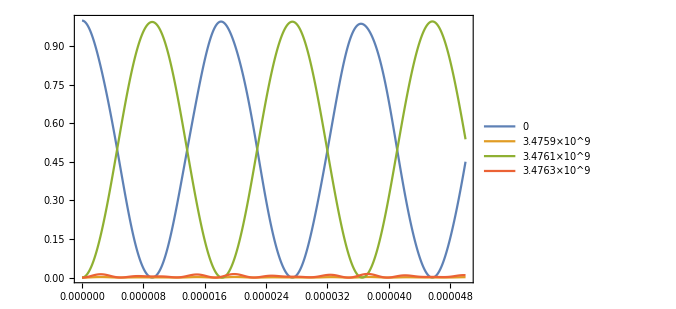

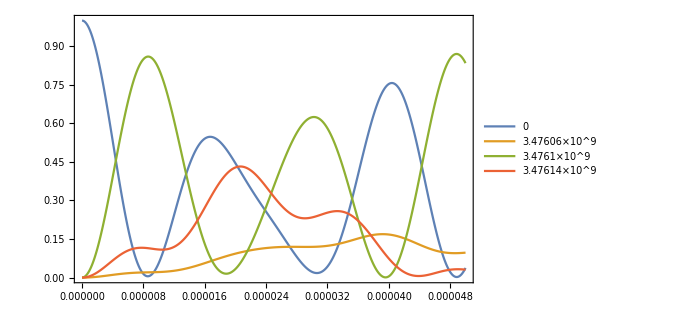

```mathematica
tS=0;tE=5 10^-5;tI=10^-7;
ListPlot[Table[(Abs[{eig[H0][[2,i]]}*.MatrixExp[-ⅈ Hrwa[vals[[3]]-vals[[1]]] t].{eig[H0][[2,1]]}ᵀ]^2)[[1,1]],{i,1,nℋN},{t,Range[tS,tE,tI]}],Joined->True,PlotRange->{0,1},PlotLegends->Table[eig[H0/(2π)][[1,i]],{i,1,nℋN}],DataRange->{tS,tE}]
```

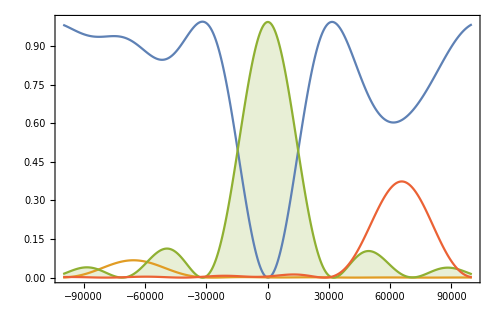

```mathematica
inst=eig[H0][[2]];
legend=Table[SphericalPlot3D[Abs[inst[[i]].yN]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,AxesLabel->{"x","y","z"},ViewPoint->{0, 0, -2},ViewVertical->{0, 1,0 },ImageSize->Tiny,Ticks->None,PlotStyle->ColorData[97,i]],{i,1,nℋN}];
ListPlot[ParallelTable[(Abs[{eig[H0][[2,i]]}*.MatrixExp[-ⅈ Hrwa[vals[[3]]-vals[[1]]+f] 0.907 10^-5].{eig[H0][[2,1]]}ᵀ]^2)[[1,1]],{i,1,nℋN},{f,-3 10^5,3 10^5,10^3}],DataRange->{-10^5,10^5},PlotRange->{0,1},PlotLegends->legend,Joined->True,Filling->{3->Axis}]
```